```mathematica
(* Normalise data *)
fileName ="laser_cont";
data =Import["C:\\p\\ann\\ex5\\"<>fileName<>".txt","CSV"];
dataT = Transpose[data];
 means=Mean/@ dataT;
sdevs = StandardDeviation/@dataT;

changeElem[x_, index_] := ((x-means[[index]])/sdevs[[index]]);
 changeRow[x_]:=(MapIndexed[changeElem,  x]); 
data = changeRow/@ data;
dataDone = N[data[[All, 1;;]]];

Export[fileName<>".csv",dataDone]
```

laser_cont.csv

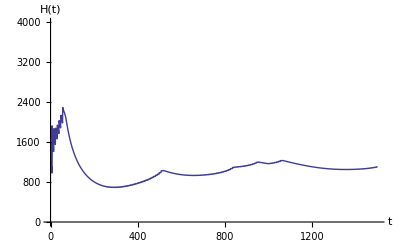

```mathematica
(* Plot energy *)
energy = ReadList["C:\\pg\\ffr135-ex5\energy.txt", {Number, Number}];ListLinePlot[energy[[1;;1500]], AxesOrigin->{0,0}, PlotRange->{0,4000}, AxesLabel->{"t","H(t)"}]
```

{«1»}

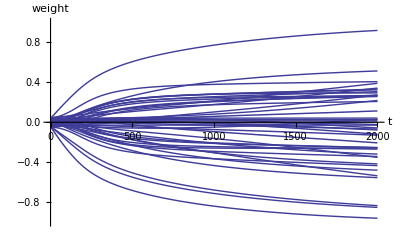

```mathematica
(* Plot weights after training *)
weights = Import["C:\\pg\\ffr135-ex5\weights.csv"]
weightsT = Transpose[weights];plots = ListLinePlot[#, AxesOrigin->{0,0}, PlotRange->{-1, 1},AxesLabel->{"t","weight"}]&/@weightsT;
Show@@plots
```

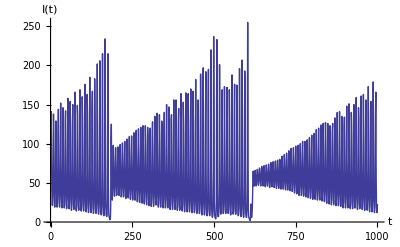

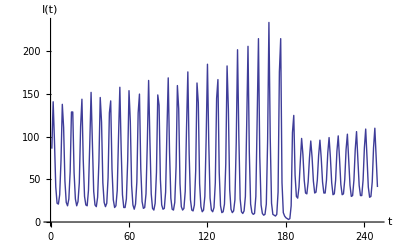

```mathematica
(* Training data *)
inputt = Transpose[ReadList["C:\\pg\\ffr135-ex5\\laser.txt", {Number}]][[1]];
ListLinePlot[inputt, AxesOrigin->{0,0},AxesLabel->{"t","I(t)"}]
ListLinePlot[inputt[[;;250]], AxesOrigin->{0,0},AxesLabel->{"t","I(t)"}]
```

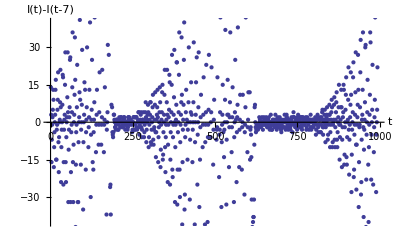

```mathematica
(* Training data diff *)
k = 7;
inputdiff = inputt[[;;1000-k]] - inputt[[k+1;;1000]];
ListPlot[inputdiff, AxesOrigin->{0,0},AxesLabel->{"t","I(t)-I(t-7)"}]
```

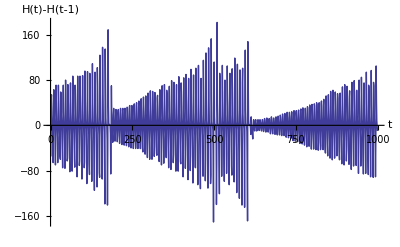

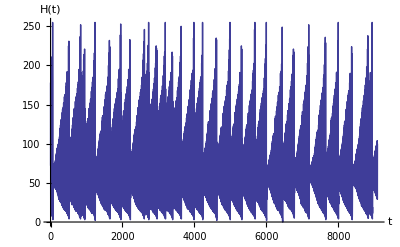

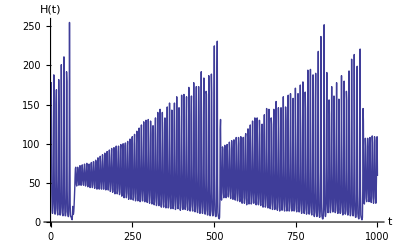

```mathematica
(* Validation data *)
inputv = Transpose[ReadList["C:\\pg\\ffr135-ex5\\laser_cont.txt", {Number}]][[1]];
ListLinePlot[inputv, AxesOrigin->{0,0},AxesLabel->{"t","H(t)"}]
ListLinePlot[inputv[[;;1000]], AxesOrigin->{0,0},AxesLabel->{"t","H(t)"}]
```

```mathematica
(* Output data *)
```

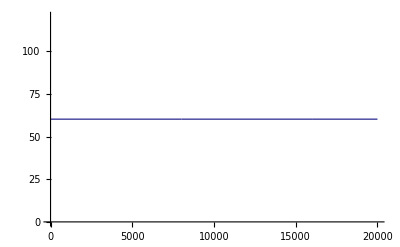

```mathematica
output = Transpose@ReadList["C:\\pg\\ffr135-ex5\\output_k1.txt", {Number}];
ListLinePlot[output]
```